## Physical constants in cgs

```mathematica
nH=1.9*10^-4;
fe=0.079;
F=vi*nH*(1+fe);
kb=1.38*10^-16;
me=9.11*10^-28;
mH=1.67*10^-24;
mHe=6.64*10^-24;
(*Bohr radius*)
a0=5.29*10^-9;
Clear[Te,THII,THI,THeII]
```

## Energy transfer rate ν_ab(σ_ab ) refers to the transferring rate when “a” is in motion and “b” is stationary

## e-HII

```mathematica
(* e-HII, NRL_Formulary_18, in 1/s, Te is in eV which is hard coded 2eV*)
Subscript[ν, eHII]=1.8*10^-19*(√(me*mH)*1^2*1^2*ne*28)/(mH*Te/11604)^(3/2);
Subscript[N, eHII]=(Subscript[ν, eHII]/ne)/(F/nH);
Subscript[N, HIIe]=Subscript[N, eHII];
```

## e-HII-HI

{{157814.,7.03317×10^-16},{126252.,7.91232×10^-16},{94688.6,8.79146×10^-16},{63125.8,1.31872×10^-15},{31562.9,1.75829×10^-15},{15781.4,2.28578×10^-15},{6312.58,3.51659×10^-15},{157.814,5.27488×10^-15}}

{a→-3.51267×10^-15,b→0.0902082,c→1.08779×10^-14}

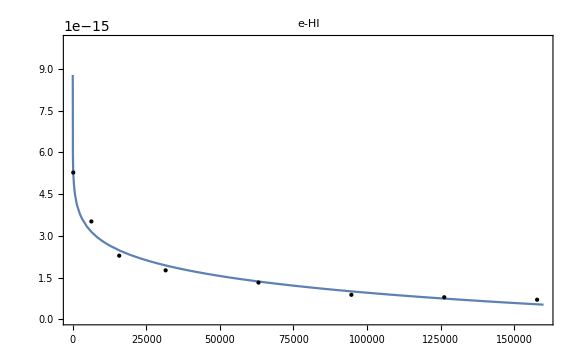

{{116040,6.7747×10^-15},{58020.,7.71539×10^-15},{31330.8,8.04507×10^-15},{11604.,8.93301×10^-15},{5802.,1.01295×10^-14},{2320.8,1.07537×10^-14},{1160.4,1.22166×10^-14},{580.2,1.46088×10^-14},{348.12,1.37112×10^-14},{290.1,1.23793×10^-14},{232.08,1.23494×10^-14},{208.872,1.36092×10^-14},{185.664,1.37419×10^-14},{174.06,1.55583×10^-14},{168.258,1.82924×10^-14},{165.357,2.0689×10^-14},{162.456,2.24666×10^-14},{159.555,2.15619×10^-14},{156.654,1.96419×10^-14},{153.753,1.84093×10^-14},{150.852,1.79302×10^-14},{147.951,1.77746×10^-14},{145.05,1.79328×10^-14},{139.248,1.87153×10^-14},{127.644,2.1009×10^-14},{121.842,2.14292×10^-14},{116.04,2.02889×10^-14},{113.719,1.94652×10^-14},{111.398,1.8586×10^-14}}

{a→-4.36556×10^-10,b→4.5057×10^-6,c→4.36583×10^-10}

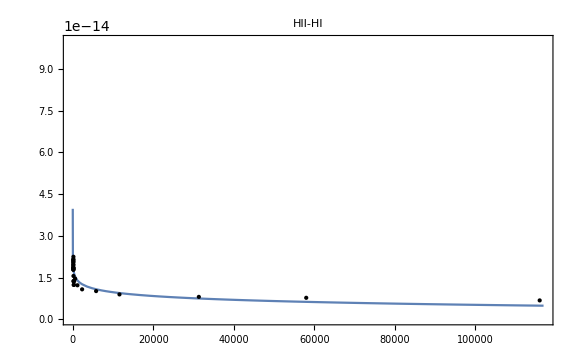

```mathematica
(* e-HI, PhysRev.112.1157, B_H_Bransden_1958_Proc._Phys._Soc._71_301*)
Subscript[σ, eHI]=-3.51267*10^-15*Te^0.0902082+1.08779*10^-14;
Subscript[σ, eHI]*√((kb*Te)/me);
Subscript[N, eHI]=(Subscript[σ, eHI]*√((kb*Te)/me))/(F/nH);
Subscript[N, HIe]=(Subscript[σ, eHI]*√((kb*Te)/me))/(F/nH);
Subscript[data, eHI]={{1*13.6*11604,8*π*a0^2},{0.8*13.6*11604,9*π*a0^2},{0.6*13.6*11604,10*π*a0^2},{0.4*13.6*11604,15*π*a0^2},{0.2*13.6*11604,20*π*a0^2},{0.1*13.6*11604,26*π*a0^2},{0.04*13.6*11604,40*π*a0^2},{0.001*13.6*11604,60*π*a0^2}}
Subscript[model, eHI]=a*t^b+c;
Subscript[fit, eHI]=FindFit[Subscript[data, eHI],Subscript[model, eHI],{a,b,c},t,MaxIterations->10000]
Subscript[model, eHIplot]=Function[{t},Evaluate[Subscript[model, eHI]/. Subscript[fit, eHI]]];
Plot[Subscript[model, eHIplot][t],{t,0,160000},Epilog->Map[Point,Subscript[data, eHI]],PlotRange->{{0,160000},{0,10^-14}},ImageSize->Large,Frame->True,LabelStyle->Directive["Label", 18],PlotLabel->"e-HI"]

(* HII-HI, rspa.1977.0051 or Draine table 2.1*)
Subscript[σ, HIIHI]=-4.36556*10^-10*THII^(4.5057*10^-6)+4.36583*10^-10;
Subscript[N, HIIHI]=(Subscript[σ, HIIHI]*√((kb*THII)/mH))/(F/nH);
Subscript[N, HIHII]=Subscript[N, HIIHI];
Subscript[data, HIIHI]={{10*11604,77.06*π*a0^2},{5.0*11604,87.76*π*a0^2},{2.7*11604,91.51*π*a0^2},{1.0*11604,101.61*π*a0^2},{0.5*11604,115.22*π*a0^2},{0.2*11604,122.32*π*a0^2},{0.1*11604,138.96*π*a0^2},{0.05*11604,166.17*π*a0^2},{0.03*11604,155.96*π*a0^2},{0.025*11604,140.81*π*a0^2},{0.02*11604,140.47*π*a0^2},{0.018*11604,154.80*π*a0^2},{0.016*11604,156.31*π*a0^2},{0.015*11604,176.97*π*a0^2},{0.0145*11604,208.07*π*a0^2},{0.01425*11604,235.33*π*a0^2},{0.014*11604,255.55*π*a0^2},{0.01375*11604,245.26*π*a0^2},{0.0135*11604,223.42*π*a0^2},{0.01325*11604,209.40*π*a0^2},{0.013*11604,203.95*π*a0^2},{0.01275*11604,202.18*π*a0^2},{0.0125*11604,203.98*π*a0^2},{0.012*11604,212.88*π*a0^2},{0.011*11604,238.97*π*a0^2},{0.0105*11604,243.75*π*a0^2},{0.01*11604,230.78*π*a0^2},{0.0098*11604,221.41*π*a0^2},{0.0096*11604,211.41*π*a0^2}}
Subscript[model, HIIHI]=a*t^b+c;
Subscript[fit, HIIHI]=FindFit[Subscript[data, HIIHI],Subscript[model, HIIHI],{a,b,c},t,MaxIterations->10000]
Subscript[model, HIIHIplot]=Function[{t},Evaluate[Subscript[model, HIIHI]/. Subscript[fit, HIIHI]]];
Plot[Subscript[model, HIIHIplot][t],{t,0,117000},Epilog->Map[Point,Subscript[data, HIIHI]],PlotRange->{{0,117000},{0,10^-13}},ImageSize->Large,Frame->True,LabelStyle->Directive["Label", 18],PlotLabel->"HII-HI"]
```

## e-HII-HI-HeI

{{23208,6.43×10^-16},{58020,5.84×10^-16},{139248,4.33×10^-16},{220476,2.92×10^-16}}

{a→-2.18539×10^-21,b→0.984171,c→6.87675×10^-16}

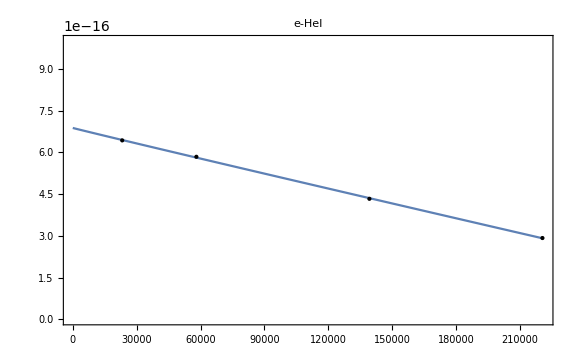

```mathematica
(* e-HeI, PhysRevA.30.1247 (1984)*)
Subscript[σ, eHeI]=-2.18539*10^-21*Te^0.984171+6.87675*10^-16;
Subscript[N, eHeI]=(Subscript[σ, eHeI]*√((kb*Te)/me))/(F/nH);
Subscript[N, HeIe]=(Subscript[σ, eHeI]*√((kb*Te)/me))/(F/nH);
Subscript[data, eHeI]={{2*11604,6.43*10^-16},{5*11604,5.84*10^-16},{12*11604,4.33*10^-16},{19*11604,2.92*10^-16}}
Subscript[model, eHeI]=a*t^b+c;
Subscript[fit, eHeI]=FindFit[Subscript[data, eHeI],Subscript[model, eHeI],{a,b,c},t,MaxIterations->10000]
Subscript[model, eHeIplot]=Function[{t},Evaluate[Subscript[model, eHeI]/. Subscript[fit, eHeI]]];
Plot[Subscript[model, eHeIplot][t],{t,0,221000},Epilog->Map[Point,Subscript[data, eHeI]],PlotRange->{{0,221000},{0,10^-15}},ImageSize->Large,Frame->True,LabelStyle->Directive["Label", 18],PlotLabel->"e-HeI"]
```

{{1.21014,3.5×10^-15},{0.774493,3.7×10^-15},{0.435652,3.9×10^-15},{0.193623,4.2×10^-15},{0.0484058,4.6×10^-15},{0.0121014,5.1×10^-15},{50000,1.×10^-18},{80000,1.×10^-19},{100000,1.×10^-20}}

{a→-5.58401×10^-11,b→5.80505×10^-6,c→5.58438×10^-11}

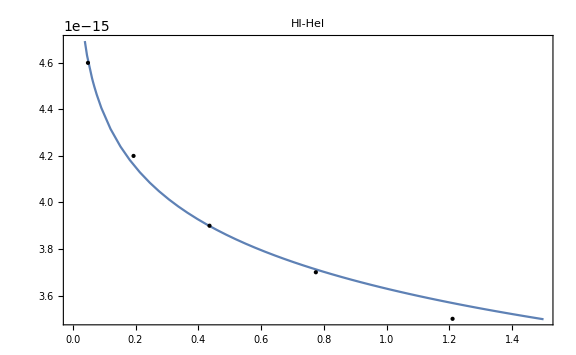

```mathematica
(* HII-HeI, Draine's table 2.1*)
Subscript[N, HIIHeI]=(1.42*10^-9)/(F/nH);
Subscript[N, HeIHII]=Subscript[N, HIIHeI];
(* HI-HeI, Draine's, PhysRevA.7.98*)
Subscript[σ, HIHeI]=-5.58401*10^-11*THI^(5.80505*10^-6)+5.58438*10^-11;
Subscript[N, HIHeI]=(Subscript[σ, HIHeI]*√((kb*THI)/mH))/(F/nH);
Subscript[N, HeIHI]=Subscript[N, HIHeI];
Subscript[data, HIHeI]={{(mH*10000^2)/kb,35.*10^-16},{(mH*8000^2)/kb,37.*10^-16},{(mH*6000^2)/kb,39.*10^-16},{(mH*4000^2)/kb,42.*10^-16},{(mH*2000^2)/kb,46.*10^-16},{(mH*1000^2)/kb,51.*10^-16},{50000,1.*10^-18},{80000,1.*10^-19},{100000,1.*10^-20}}
Subscript[model, HIHeI]=a*t^b+c;
Subscript[fit, HIHeI]=FindFit[Subscript[data, HIHeI],Subscript[model, HIHeI],{a,b,c},t,MaxIterations->10000]
Subscript[model, HIHeIplot]=Function[{t},Evaluate[Subscript[model, HIHeI]/. Subscript[fit, HIHeI]]];
Plot[Subscript[model, HIHeIplot][t],{t,0,1.5},Epilog->Map[Point,Subscript[data, HIHeI]],PlotRange->Automatic,ImageSize->Large,Frame->True,LabelStyle->Directive["Label", 18],PlotLabel->"HI-HeI"]
```

## e-HII-HI-HeI-HeII

```mathematica
(* e-HeII, NRL_Formulary_18.pdf p33, in sec^-1, T is in eV which is hard coded 2eV*)
Subscript[ν, eHeII]=1.8*10^-19*(√(me*mHe)*1^2*2^2*ne*28)/(mHe*Te/11604)^(3/2);
Subscript[N, eHeII]=(Subscript[ν, eHeII]/ne)/(F/nH);
Subscript[N, HeIIe]=Subscript[N, eHeII];
```

{{11.604,5.4×10^-15},{116.04,4.5×10^-15},{1160.4,3.7×10^-15},{11604.,2.8×10^-15},{116040.,2.1×10^-15},{1.1604×10^6,1.5×10^-15},{1.1604×10^7,1.×10^-15}}

{a→-7.71569×10^-11,b→4.18115×10^-6,c→7.71629×10^-11}

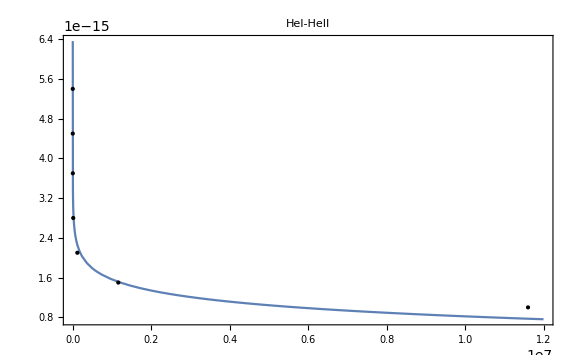

```mathematica
(* HII-HeII, NRL_Formulary_18.pdf p33, in sec^-1, T is in eV which is hard coded 2eV*)
Subscript[ν, HIIHeII]=1.8*10^-19*((√(mH*mHe)*1^2*2^2*nHII*20*10^(27*1.5))/(mHe*THII/11604*10^27+mH*THeII/11604*10^27)^(3/2));
Subscript[N, HIIHeII]=(Subscript[ν, HIIHeII]/nHII)/(F/nH);
Subscript[N, HeIIHII]=Subscript[N, HIIHeII];
(* HI-HeII, Draine's table 2.1*)
Subscript[μ, relHI]=(mH*mHe)/(mH+mHe)/((mH*mHe)/(mH+mHe));
Subscript[N, HIHeII]=Subscript[N, HIIHeI]*1*(4.5/1.383)^(1/2)*(1/Subscript[μ, relHI]);
Subscript[N, HeIIHI]=Subscript[N, HIHeII];
(* HeI-HeII, Draine's table 2.1, 2017_PoP_Kz_ia_1*)
Subscript[σ, HeIHeII]=-7.71569*10^-11*THeII^(4.18115*10^-6)+7.71629*10^-11;
Subscript[N, HeIHeII]=(Subscript[σ, HeIHeII]*√((kb*THeII)/mHe))/(F/nH);
Subscript[N, HeIIHeI]=Subscript[N, HeIHeII];
Subscript[data, HeIIHeI]={{10^-3*11604.,54.*10^-16},{10^-2*11604.,45.*10^-16},{10^-1*11604.,37.*10^-16},{1*11604.,28.*10^-16},{10*11604.,21.*10^-16},{10^2*11604.,15.*10^-16},{10^3*11604.,10.*10^-16}}
Subscript[model, HeIIHeI]=a*t^b+c;
Subscript[fit, HeIIHeI]=FindFit[Subscript[data, HeIIHeI],Subscript[model, HeIIHeI],{a,b,c},t,MaxIterations->10000]
Subscript[model, HeIIHeIplot]=Function[{t},Evaluate[Subscript[model, HeIIHeI]/. Subscript[fit, HeIIHeI]]];
Plot[Subscript[model, HeIIHeIplot][t],{t,0.1,12000000},Epilog->Map[Point,Subscript[data, HeIIHeI]],PlotRange->All,ImageSize->Large,Frame->True,LabelStyle->Directive["Label", 18],PlotLabel->"HeI-HeII"]
```

## Print all interaction rates (e.g. N_eHII is equivalent to nuTeTHII in the code)

```mathematica
Print[Style["Ν_eHII= ",24],Style[Subscript[N, eHII],24]]
Print[Style["------",24]]
Print[Style["Ν_eHI= ",24],Style[Subscript[N, eHI],24]]
Print[Style["Ν_HIIHI= ",24],Style[Subscript[N, HIIHI],24]]
Print[Style["------",24]]
Print[Style["Ν_eHeI= ",24],Style[Subscript[N, eHeI],24]]
Print[Style["Ν_HIIHeI= ",24],Style[Subscript[N, HIIHeI],24]]
Print[Style["Ν_HIHeI= ",24],Style[Subscript[N, HIHeI],24]]
Print[Style["------",24]]
Print[Style["Ν_eHeII= ",24],Style[Subscript[N, eHeII],24]]
Print[Style["Ν_HIIHeII= ",24],Style[Subscript[N, HIIHeII],24]]
Print[Style["Ν_HIHeII= ",24],Style[Subscript[N, HIHeII],24]]
Print[Style["Ν_HeIHeII= ",24],Style[Subscript[N, HeIHeII],24]]
```

Ν_eHII= 0.105527/(Te^(3/2) vi)

------

Ν_eHI= (360711. (1.08779×10^-14-3.51267×10^-15 Te^0.0902082) √Te)/vi

Ν_HIIHI= (8424.81 (4.36583×10^-10-4.36556×10^-10 THII^(4.5057×10^-6)) √THII)/vi

------

Ν_eHeI= (360711. (6.87675×10^-16-2.18539×10^-21 Te^0.984171) √Te)/vi

Ν_HIIHeI= (1.31603×10^-9)/vi

Ν_HIHeI= (8424.81 (5.58438×10^-11-5.58401×10^-11 THI^(5.80505×10^-6)) √THI)/vi

------

Ν_eHeII= 0.106163/(Te^(3/2) vi)

Ν_HIIHeII= 1.40535/((0.143916 THeII+0.572216 THII)^(3/2) vi)

Ν_HIHeII= (2.3739×10^-9)/vi

Ν_HeIHeII= (4225.07 (7.71629×10^-11-7.71569×10^-11 THeII^(4.18115×10^-6)) √THeII)/vi

```mathematica
ClearAll[Subscript]
M5={{-Subscript[Ν, eHII]-Subscript[Ν, eHeI]-Subscript[Ν, eHI]-Subscript[Ν, eHeII],Subscript[Ν, eHII],Subscript[Ν, eHI],Subscript[Ν, eHeI],Subscript[Ν, eHeII]},
{Subscript[Ν, eHII],-Subscript[Ν, eHII]-Subscript[Ν, HIIHeI]-Subscript[Ν, HIIHI]-Subscript[Ν, HIIHeII],Subscript[Ν, HIIHI],Subscript[Ν, HIIHeI],Subscript[Ν, HIIHeII]},
{Subscript[Ν, eHI],Subscript[Ν, HIIHI],-Subscript[Ν, eHI]-Subscript[Ν, HIHeI]-Subscript[Ν, HIIHI]-Subscript[Ν, HIHeII],Subscript[Ν, HIHeI],Subscript[Ν, HIHeII]},
{Subscript[Ν, eHeI], Subscript[Ν, HIIHeI],Subscript[Ν, HIHeI],-Subscript[Ν, eHeI]-Subscript[Ν, HIHeI]-Subscript[Ν, HIIHeI]-Subscript[Ν, HeIHeII],Subscript[Ν, HeIHeII]},
{Subscript[Ν, eHeII],Subscript[Ν, HIIHeII],Subscript[Ν, HIHeII],Subscript[Ν, HeIHeII],-Subscript[Ν, eHeII]-Subscript[Ν, HIIHeII]-Subscript[Ν, HIHeII]-Subscript[Ν, HeHeII]}};
Print[Style["M5=",24],Style[MatrixForm[M5],24]]
Print[Style["(1-M5Δt)=",24],Style[MatrixForm[Simplify[IdentityMatrix[5]-M5*Δt]],24]]
```

M5=(-Ν_eHeI-Ν_eHeII-Ν_eHI-Ν_eHII | Ν_eHII | Ν_eHI | Ν_eHeI | Ν_eHeII
Ν_eHII | -Ν_eHII-Ν_HIIHeI-Ν_HIIHeII-Ν_HIIHI | Ν_HIIHI | Ν_HIIHeI | Ν_HIIHeII
Ν_eHI | Ν_HIIHI | -Ν_eHI-Ν_HIHeI-Ν_HIHeII-Ν_HIIHI | Ν_HIHeI | Ν_HIHeII
Ν_eHeI | Ν_HIIHeI | Ν_HIHeI | -Ν_eHeI-Ν_HeIHeII-Ν_HIHeI-Ν_HIIHeI | Ν_HeIHeII
Ν_eHeII | Ν_HIIHeII | Ν_HIHeII | Ν_HeIHeII | -Ν_eHeII-Ν_HeHeII-Ν_HIHeII-Ν_HIIHeII)

(1-M5Δt)=(1+Δt Ν_eHeI+Δt Ν_eHeII+Δt Ν_eHI+Δt Ν_eHII | -Δt Ν_eHII | -Δt Ν_eHI | -Δt Ν_eHeI | -Δt Ν_eHeII
-Δt Ν_eHII | 1+Δt Ν_eHII+Δt Ν_HIIHeI+Δt Ν_HIIHeII+Δt Ν_HIIHI | -Δt Ν_HIIHI | -Δt Ν_HIIHeI | -Δt Ν_HIIHeII
-Δt Ν_eHI | -Δt Ν_HIIHI | 1+Δt Ν_eHI+Δt Ν_HIHeI+Δt Ν_HIHeII+Δt Ν_HIIHI | -Δt Ν_HIHeI | -Δt Ν_HIHeII
-Δt Ν_eHeI | -Δt Ν_HIIHeI | -Δt Ν_HIHeI | 1+Δt Ν_eHeI+Δt Ν_HeIHeII+Δt Ν_HIHeI+Δt Ν_HIIHeI | -Δt Ν_HeIHeII
-Δt Ν_eHeII | -Δt Ν_HIIHeII | -Δt Ν_HIHeII | -Δt Ν_HeIHeII | 1+Δt Ν_eHeII+Δt Ν_HeHeII+Δt Ν_HIHeII+Δt Ν_HIIHeII)

```mathematica
ClearAll;
```